```mathematica
dispersion[x_,y_] := -2*(Cos[x]+Cos[y])-4*tp*Cos[x]*Cos[y]
```

```mathematica
tp = -0.15;
mu = 8*(tp-2*tp^3);
```

```mathematica
mu
```

-1.146

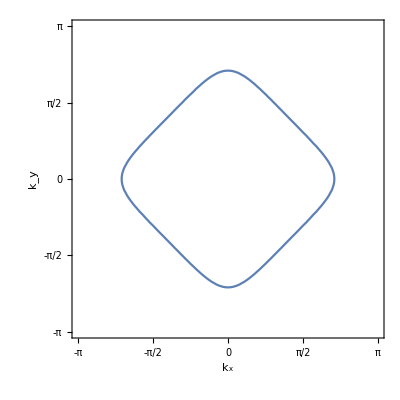

```mathematica
ContourPlot[dispersion[x,y]==mu,{x,-Pi,Pi},{y,-Pi,Pi},Frame->True,FrameStyle->Black,FrameLabel->{"k_x","k_y"},FrameTicks -> {{{-Pi,-Pi/2,0,Pi/2,Pi},None},{{-Pi,-Pi/2,0,Pi/2,Pi},None}}]
```

```mathematica
Solve[dispersion[x,x]==mu,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-1.2661},{x→0.-2.538 ⅈ},{x→0.+2.538 ⅈ},{x→1.2661}}

```mathematica
pt = 1.2661;
```

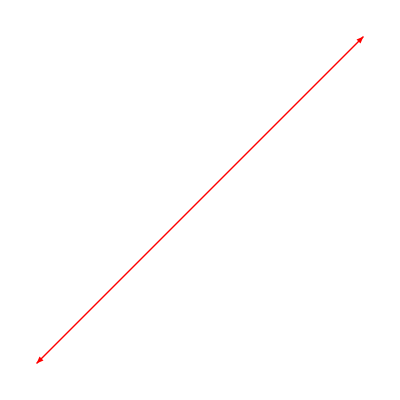

```mathematica
Graphics[{Red,Arrowheads[{-.1,.1}],Arrow[{{-pt,-pt},{pt,pt}}]}]
```

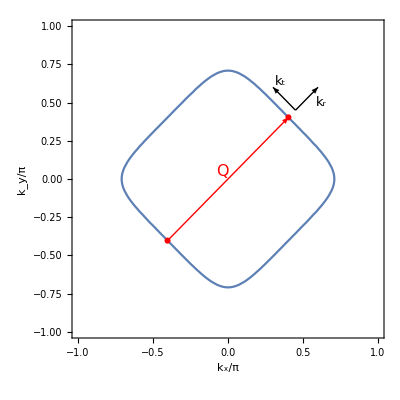

```mathematica
Show[{ContourPlot[dispersion[Pi*x,Pi*y]==mu,{x,-1,1},{y,-1,1},ContourStyle->bl,Frame->True,FrameStyle->Black,FrameLabel->{Style["k_x/π",19,Black,FontFamily->"Times"],Style["k_y/π",19,Black,FontFamily->"Times"]},LabelStyle->Black,FrameTicks -> {Style[{{-1.0,-0.5,0.0,0.5,1.0},None},{{-1,-0.5,0,0.5,1},None}],19}],
Graphics[{Red,Disk[{-pt/Pi,-pt/Pi},0.02]}],
Graphics[{Red,Disk[{pt/Pi,pt/Pi},0.02]}],Graphics[{Red,Arrowheads[{0,.05}],Arrow[{{-pt/Pi,-pt/Pi},{pt/Pi,pt/Pi}}],Text[Style["Q",16,FontFamily->"Times"],{-0.04,0.05}]}],Graphics[{Black,Arrowheads[{0,.03}],Arrow[{{0.45,0.45},{0.6,0.6}}],Text[Style["k_r",13,FontFamily->"Times"],{0.62,0.5}]}],Graphics[{Black,Arrowheads[{0,.03}],Arrow[{{0.45,0.45},{0.3,0.6}}],Text[Style["k_t",13,FontFamily->"Times"],{0.35,0.64}]}]}]
```

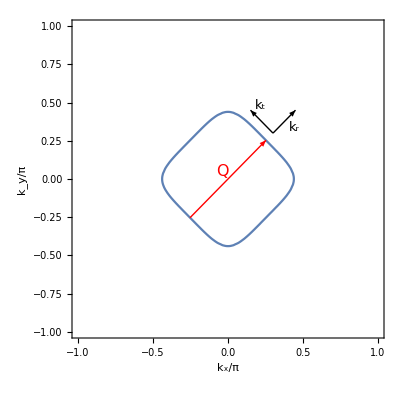

```mathematica
Show[{ContourPlot[dispersion[Pi*x,Pi*y]==mu,{x,-1,1},{y,-1,1},ContourStyle->bl,Frame->True,FrameStyle->Black,FrameLabel->{Style["k_x/π",19,Black,FontFamily->"Times"],Style["k_y/π",19,Black,FontFamily->"Times"]},LabelStyle->Black,FrameTicks -> {Style[{{-1.0,-0.5,0.0,0.5,1.0},None},{{-1,-0.5,0,0.5,1},None}],19}],Graphics[{Red,Arrowheads[{0,.05}],Arrow[{{-pt/Pi,-pt/Pi},{pt/Pi,pt/Pi}}],Text[Style["Q",16,FontFamily->"Times"],{-0.04,0.05}]}],Graphics[{Black,Arrowheads[{0,.03}],Arrow[{{0.3,0.3},{0.45,0.45}}],Text[Style["k_r",13,FontFamily->"Times"],{0.44,0.34}]}],Graphics[{Black,Arrowheads[{0,.03}],Arrow[{{0.3,0.3},{0.15,0.45}}],Text[Style["k_t",13,FontFamily->"Times"],{0.22,0.48}]}]}]
```

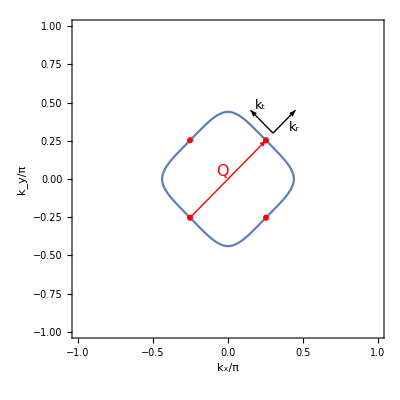

```mathematica
Show[{ContourPlot[dispersion[Pi*x,Pi*y]==mu,{x,-1,1},{y,-1,1},ContourStyle->bl,Frame->True,FrameStyle->Black,FrameLabel->{Style["k_x/π",19,Black,FontFamily->"Times"],Style["k_y/π",19,Black,FontFamily->"Times"]},LabelStyle->Black,FrameTicks -> {Style[{{-1.0,-0.5,0.0,0.5,1.0},None},{{-1,-0.5,0,0.5,1},None}],19}],Graphics[{Red,Arrowheads[{0,.05}],Arrow[{{-pt/Pi,-pt/Pi},{pt/Pi,pt/Pi}}],Text[Style["Q",16,FontFamily->"Times"],{-0.04,0.05}]}],Graphics[{Red,Disk[{-pt/Pi,-pt/Pi},0.02]}],
Graphics[{Red,Disk[{pt/Pi,pt/Pi},0.02]}],Graphics[{Red,Disk[{pt/Pi,-pt/Pi},0.02]}],Graphics[{Red,Disk[{-pt/Pi,pt/Pi},0.02]}],Graphics[{Black,Arrowheads[{0,.03}],Arrow[{{0.3,0.3},{0.45,0.45}}],Text[Style["k_r",13,FontFamily->"Times"],{0.44,0.34}]}],Graphics[{Black,Arrowheads[{0,.03}],Arrow[{{0.3,0.3},{0.15,0.45}}],Text[Style["k_t",13,FontFamily->"Times"],{0.22,0.48}]}]}]
```

```mathematica
backgr = GrayLevel[0.3]
```

GrayLevel[0.3]

```mathematica
yellow = RGBColor[217,165,0]
```

RGBColor[217, 165, 0]

```mathematica
CMYKColor[10,40,98,2]
```

CMYKColor[10, 40, 98, 2]

```mathematica
RGBColor["#D9A500"]
```

RGBColor[0.8509803921568627, 0.6470588235294118, 0.]

```mathematica
(**)
```

```mathematica
lightblue = RGBColor[110,206,178]
```

RGBColor[110, 206, 178]

```mathematica
CMYKColor[57,0,40,0]
```

CMYKColor[57, 0, 40, 0]

```mathematica
(**)
```

```mathematica
ruby = RGBColor[123,5,69]
```

RGBColor[123, 5, 69]

```mathematica
CMYKColor[33,95,32,0]
```

CMYKColor[33, 95, 32, 0]

```mathematica
pred = RGBColor[170,0,0]
```

RGBColor[170, 0, 0]

```mathematica
rblue = RGBColor[0,127,186]
```

RGBColor[0, 127, 186]

```mathematica
RGBColor["#007FBA"]
```

RGBColor[0., 0.4980392156862745, 0.7294117647058823]